# Examination of the DC Coils Contrasts

```mathematica
Needs["ErrorBarPlots`"]
```

## Data Import

```mathematica
files=FileNames["*dc*.dat",NotebookDirectory[]]
data=Import[#]&/@files;
```

{C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 26.11.2018\2018-11-26-1115-scan-dc1coil.dat,C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 26.11.2018\2018-11-26-1200-scan-dc2coil.dat,C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 26.11.2018\2018-11-26-1300-scan-dc1coil.dat,C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 26.11.2018\2018-11-26-1345-scan-dc2coil.dat,C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 26.11.2018\2018-11-26-1430-scan-dc1coil.dat,C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 26.11.2018\2018-11-26-1530-scan-dc1coilright.dat}

## Data Cleaning & Error Calculation

```mathematica
data=Transpose[Transpose[#[[5;;-1]]][[1;;2]]]&/@data;
```

```mathematica
error=Map[ErrorBar,Re[Sqrt[Transpose[#][[2]]]]]&/@data ;
dataError=Partition[Riffle[data[[#]],error[[#]]],2]&/@Range[Length[data]];
```

## Plotting the Data

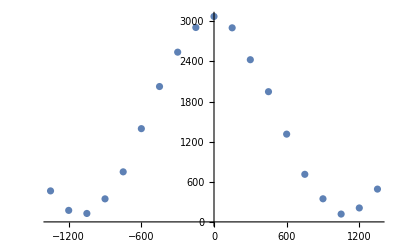
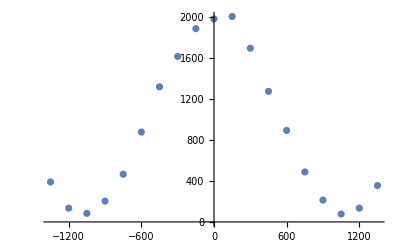
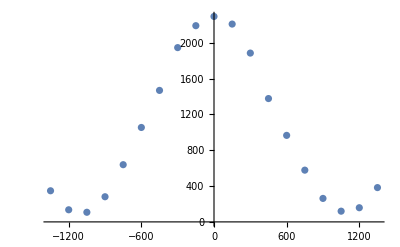
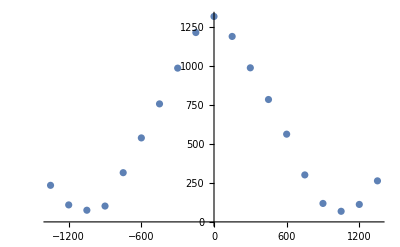
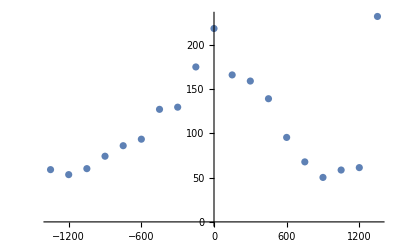
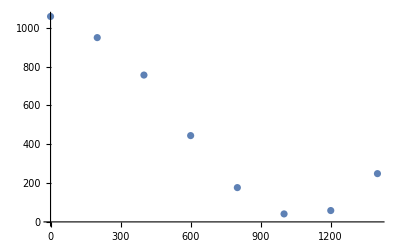

```mathematica
dPlots=ListPlot[#,PlotRange->All]&/@data
```

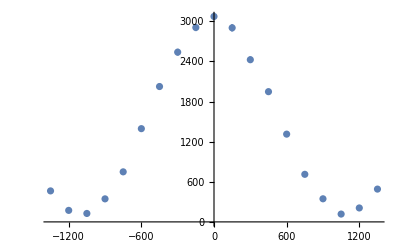
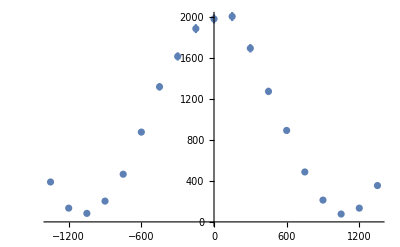
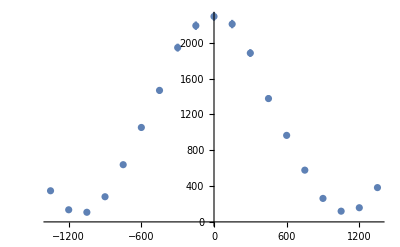
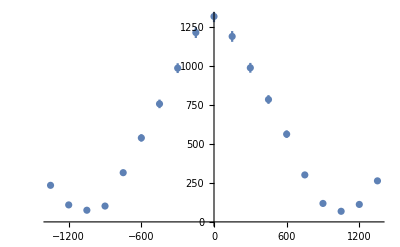
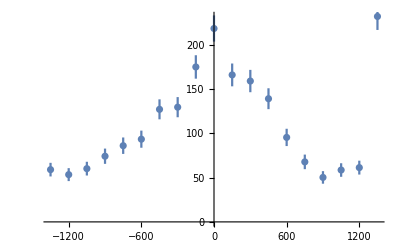
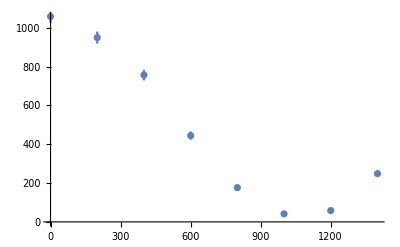

```mathematica
ePlots=ErrorListPlot[#,PlotRange->All]&/@dataError
```

## Fit

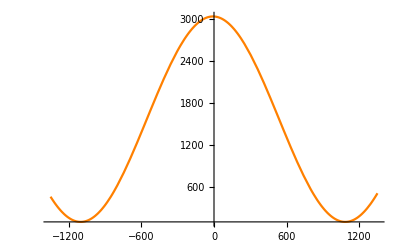
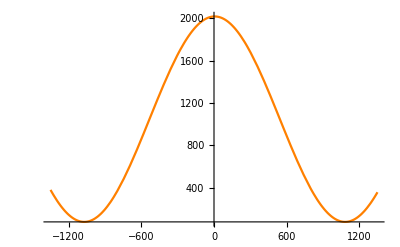
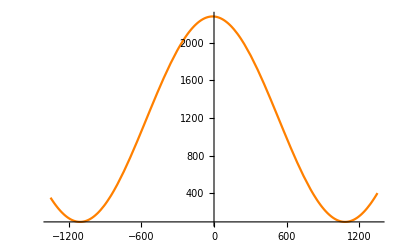
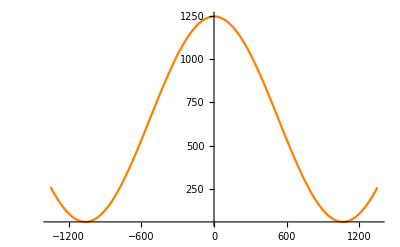
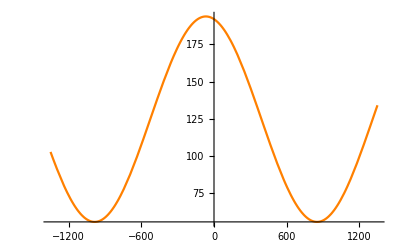
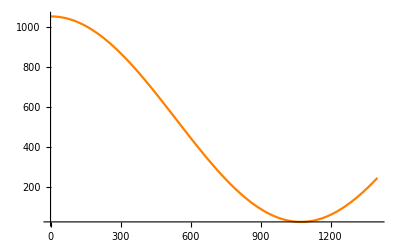

```mathematica
model=A*Cos[ω*x+ϕ]+B;
startValues={{A,3000},{ω,π/1000},{ϕ,0},{B,1500}};
xMin=Min[Transpose[#][[1]]]&/@data;
xMax=Max[Transpose[#][[1]]]&/@data;

fit=FindFit[#,model,startValues,x]&/@data;

fPlots=Plot[Evaluate[model/.fit[[#]]],{x,xMin[[#]],xMax[[#]]},PlotRange->All,PlotStyle->Orange]&/@Range[Length[fit]]
```

A→1462.78 | ω→0.00287558 | ϕ→0.0247957 | B→1570.4
A→970.504 | ω→0.00291636 | ϕ→-0.0160565 | B→1048.23
A→1092.45 | ω→0.00287115 | ϕ→0.0332157 | B→1187.63
A→595.443 | ω→0.00295507 | ϕ→-0.00293003 | B→652.678
A→69.1517 | ω→0.00342084 | ϕ→0.230105 | B→124.644
A→512.808 | ω→0.00293791 | ϕ→-0.00839163 | B→539.222

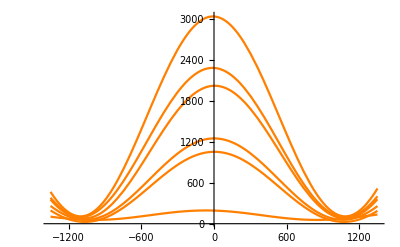

```mathematica
fit2=fit//TableForm
Plot[Evaluate[model/.fit2[[#]]],{x,xMin[[#]],xMax[[#]]},PlotRange->All,PlotStyle->Orange]&/@Range[Length[fit2]]//TableForm
```

## Data & Fit Plots

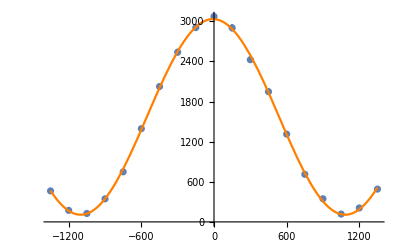
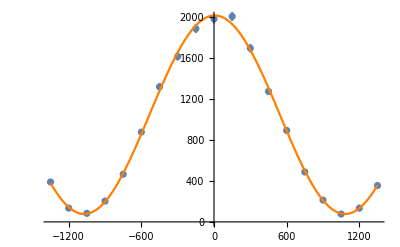
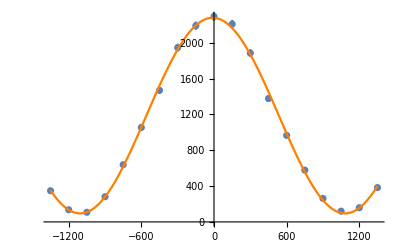
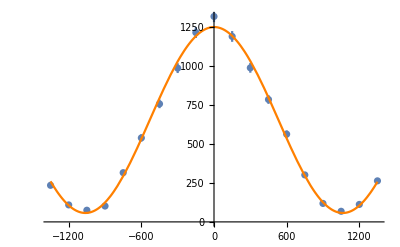
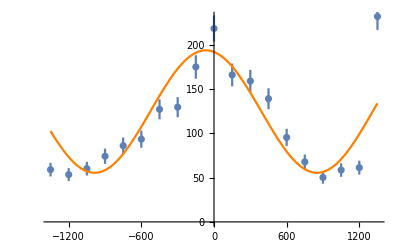
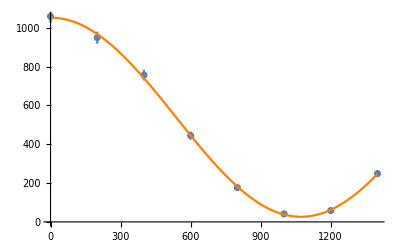

```mathematica
Show[ePlots[[#]],fPlots[[#]]]&/@Range[Length[data]]
```

## Contrast

Definition of contrast and its error.

```mathematica
Contrast[Imax_,Imin_]:=(Imax-Imin)/(Imax+Imin)
ErrContrast[Imax_,Imin_,ΔImax_,ΔImin_]:=Sqrt[(((2*Imin)/(Imax+Imin)^2)*ΔImax)^2+(((-2*Imax)/(Imax+Imin)^2)*ΔImin)^2]
```

Finding the maxima and minima of fit.

```mathematica
Imax=(model/.#&/@fit)/.{x->0};
Imin=model/.#&/@Transpose[Join[Transpose[fit],{x->π/#[[2]][[2]]&/@fit}]];
```

Calculating contrast and its error.

```mathematica
contrast=Contrast@@#&/@Partition[Riffle[Imax,Imin],2];
contrastD=ErrContrast@@#&/@Partition[Riffle[Riffle[Imax,Sqrt[Imax]],Riffle[Imin,Sqrt[Imin]]],4];
Transpose[{contrast,contrastD}]//TableForm
```

0.931185 | 0.00650479
0.925728 | 0.00825975
0.919356 | 0.00807252
0.912304 | 0.0113346
0.54017 | 0.0533006
0.950981 | 0.00941697